## Chap 14

### 14-1

#### phase_diagram

```mathematica
Block[{lt=0.8,col,bdy},
col=<|"g"->LightBlue,"l"->Blue,"s"->Green|>;
bdy=<|"sg"->BSplineCurve[{{0,0},{0.1,0},{0.6,0.3},{1,1}}],"lg"->BSplineCurve[{{1,1},{2.5,1.5},{3,3}}],"sl"->Line[{{1,1},{1.1,4}}]|>;
Graphics[{{Lighter[col["s"],lt],FilledCurve[{bdy["sg"],bdy["sl"],Line[{{1.1,4},{0,4}}]}]},
{Lighter[col["l"],lt],FilledCurve[{bdy["lg"],Line[{{3.3,4},{1.1,4}}]}]},
{Lighter[col["g"],lt],FilledCurve[{bdy["sg"],bdy["lg"],Line[{{4,4},{4,0}}]}]},
Block[{dx=0.1,h=1,s=0.3,w=0.7},Translate[{EdgeForm[None],Table[{Blend[Lighter[col[#],lt]&/@{"l","g"},(x+1)/2],Triangle[{{0,0},{s+w x,h},{s+w(x+dx),h}}]},{x,-1,1-dx,dx}]},bdy["lg"][[1,-1]]]],
{Arrowheads[0.05],Arrow[{{0,0},#}]&/@{{4,0},{0,4}},Text["Temperature \!\(T\)",{2,0},{0,1}],Text["Pressure \!\(p\)",{0,2},{0,-1},{0,1}]},
{AbsoluteThickness[1.5],bdy["sg"],bdy["lg"],bdy["sl"]},{AbsolutePointSize[5],Point[{bdy["lg"][[1,1]],bdy["lg"][[1,-1]]}]},
{Text["Solid",{0.5,2}],Text["Liquid",{1.8,2.5}],Text["Gas",{3,1}],
Text[Style["Supercritical\nfluid",12,LineSpacing->{0,12}],{3,3.5}],Text[Style["Triple\npoint",12,LineSpacing->{0,12}],{1,1},{-1,1.2}],
Text[Style["Critical\npoint",12,LineSpacing->{0,12}],{3,3},{-1,1.2}]}},PlotRange->{{-0.5,4},{-0.5,4}},Frame->False,ImageSize->180]]
```

-Graphics-

```mathematica
Block[{lt=0.8,col,bdy},
col=<|"g"->White,"l"->Blue,"s"->Green|>;
bdy=<|"sg"->BSplineCurve[{{0,0},{0.1,0},{0.6,0.3},{1,1}}],"lg"->BSplineCurve[{{1,1},{2.5,1.5},{3,3}}],"sl"->Line[{{1,1},{0.4,4}}]|>;
Graphics[{{Lighter[col["s"],lt],FilledCurve[{bdy["sg"],bdy["sl"],Line[{{0.4,4},{0,4}}]}]},
{Lighter[col["l"],lt],FilledCurve[{bdy["lg"],Line[{{3.3,4},{0.4,4}}]}]},
Block[{dx=0.1,h=1,s=0.3,w=0.4},Translate[{EdgeForm[None],Table[{Blend[Lighter[col[#],lt]&/@{"l","g"},(x+1)/2],Triangle[{{0,0},{s+w x,h},{s+w(x+dx),h}}]},{x,-1,1-dx,dx}]},bdy["lg"][[1,-1]]]],
{Opacity[0.2],AbsoluteThickness[1],Line[{{0,3},{3,3},{3,0}}],Line[{{{0,2},{4,2}},{{0.8,0},{0.8,2}},{{2.5,2},{2.5,0}}}],Line[{{0,1},{1,1},{1,0}}]},
{AbsoluteThickness[1.5],bdy["sg"],bdy["lg"],bdy["sl"]},{AbsolutePointSize[5],Point[{bdy["lg"][[1,1]],bdy["lg"][[1,-1]]}]},
{Text[Style["Ice\n(solid)",LineSpacing->{0, 12}],{0.5,1.3}],Text[Style["Water\n(liquid)",LineSpacing->{0,12}],{1.8,2.5}],Text[Style["Vapor\n(gas)",LineSpacing->{0,12}],{2.5,0.8}],
Text[Style["Supercritical\nfluid",12,LineSpacing->{0,10}],{3,3.5}],Text[Style["Triple\npoint",10,LineSpacing->{0,8}],{1,1},{-1,1.2}],
Text[Style["Critical\npoint",10,LineSpacing->{0,8}],{3,3},{-1,1.2}]}},PlotRange->{{0,4},{0,4}},Frame->True,FrameTicks->{{{{1,"0.6"},{2,"101"},{3,"\!\(2×10\^4\)"}},{{2,"1 atm"}}},{{{0.8,"0"},{1,""},{1.2,Rotate["0.01",-π/4],{0,0}},{2.5,Rotate["100",-π/4]},{3,Rotate["374",-π/4]}},None}},FrameLabel->{"\!\(T\) [°C]","\!\(P\) [kPa]"},ImageSize->250]]
```

-Graphics-

## Chap 15

### 15-1

#### angular

##### Definition

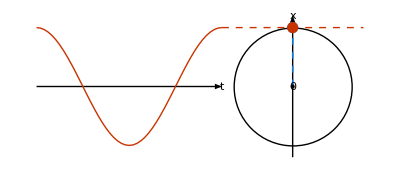

```mathematica
Block[{t=0},
Graphics[{{Circle[{0,0}],Arrowheads[0.03],Arrow[{{0,1.2 #}&/@{-1,1}}],Text["\!\(x\)",{0,1.2},{2,0}],Translate[{Arrow[{{#,0}&/@{-π,0}}],Text["\!\(t\)",{0,0},{-1.5,0}]},{-1.2,0}]},{AbsolutePointSize[8],Dashed,{Red,Line[{#,Cos[t]}&/@{-1.2,1.2}]},{Blue,Line[{{0,0},{-Sin[t],Cos[t]}}],Point[{-Sin[t],Cos[t]}]},{Red, Point[{0,Cos[t]}]}},{Point[{0,0}],Text["0",{0,0},{2,0.2}]},Translate[{Red,Line[Table[{u,Cos[t+2u]},{u,-π,0,π/48}]]},{-1.2,0}]},ImageSize->{Automatic,150}]]
```

## Chap 32

### 32-1

#### manifolds

```mathematica
Block[{pts,bsf},
SeedRandom[6];
pts=Table[Block[{δr,δθ,δh},
{δr,δθ,δh}={0.2r^4,0.2π,0.2r^4}RandomReal[{-1,1},3];
{(r+δr) Cos[θ+δθ],(r+δr) Sin[θ+δθ],-0.5r^4Sin[θ]^2+δh }],{θ,0,3π/2,π/2},{r,{0,0.1,0.5,1}}];
bsf=BSplineFunction[pts,SplineClosed->{True,False}];
Graphics3D[{{Opacity[0.8],Lighter[Red,0.65],EdgeForm[Blue],BSplineSurface[pts,SplineClosed->{True,False}]},{Red,Text["\!\(Σ\)",{0.3,-0.4,-0.2}],Blue,Text["\!\(∂Σ\)",{0.25,-0.8,-0.55}]},
{Red,Arrowheads[0.05],Block[{n},n=Normalize[Cross[Derivative[0,1][bsf][##],Derivative[1,0][bsf][##]]];
Translate[Arrow[Tube[{{0,0,0},0.18n},0.01]],bsf[##]]]&@@@{{0,0.01},{0.8,0.7},{0.4,0.8}},Text["\!\(n\&^\)",bsf[0,0],{1.5,-0.8}]},{Blue,EdgeForm[None],Translate[Cone[{{0,0,0},0.12Normalize[bsf[#+0.001,1]-bsf[#,1]]},0.03],bsf[#-0.01,1]]&/@{0.4,0.7}}},Lighting->"Neutral",Boxed->False,ViewPoint->{1.6,-2,1.2},AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{surf},
surf=Cases[ParametricPlot3D[(0.5+0.5Sin[θ]^4){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},Mesh->{5,Range[0,2π,π/4]+0.001}],
GraphicsComplex[pts_,p_,opts__]:>
{GraphicsComplex[pts,{{Opacity[0.8],Lighter[Red,0.7],EdgeForm[None],Cases[p,g_GraphicsGroup:>g,∞]},
{Red,Opacity[0.2],AbsoluteThickness[1],Dashed,Cases[p,_Line,∞]}},opts],
{Red,Arrowheads[0.04],Translate[Arrow[Tube[{{0,0,0},0.3#2},0.012]],#1]&@@@(Thread@{pts,OptionValue[opts,VertexNormals]})[[{1,6,11}]],
Text["\!\(n\&^\)",pts[[1]],{1.5,-1.5}]}},∞];
SeedRandom[0];
Graphics3D[{surf,{Red,Text["\!\(S\)",{1,0,0}]}},Lighting->{"Neutral",DirectionalLight[Gray,{2,-1,-2}]},Boxed->False,ViewPoint->{4,-2,2},PlotRange->All,AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{pts},
SeedRandom[1];
pts=Table[{x,0,0}+0.2(x^2-1)RandomReal[{-1,1},3],{x,{-1,-0.5,0,0.5,1}}];
Graphics3D[{{Blue,Arrowheads[{0.06,#}&/@{0.3,0.8}],Arrow[Tube[BSplineCurve[pts],0.02]],Text["\!\(Γ\)",{0,0,0},{0,-1}],Text["\!\(ℓ\&^\)",{-0.6,0,0},{0,1}]},
{Purple,Point[{#,-0.1,0.1}]&/@{-1,1},Text["\!\(a\)",{-1,0,0},{0,-0.8}],Text["\!\(b\)",{1,0,0},{0,-0.8}]}},Lighting->"Neutral",Boxed->False,PlotRange->{{-1.1,1.1},{-1,1},{-1,1}},ViewPoint->{0,-4,4},AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{pts},
SeedRandom[5];
pts=Table[{Cos[θ],Sin[θ],0}+0.2RandomReal[{-1,1},3],{θ,0,5π/6,π/6}];
Graphics3D[{{Blue,Arrowheads[{0.07,#}&/@{0,0.33,0.66}],Arrow[Tube[BSplineCurve[pts,SplineClosed->True],0.015]],Text["\!\(C\)",{0,0,0},{0,-0.8}],Text["\!\(ℓ\&^\)",{0,0,0},{-6,2.5}]}},Lighting->"Neutral",Boxed->False,ViewPoint->{1,2,4},AspectRatio->1,ImageSize->100]]
```

-Graphics3D-

##### Backup (with field lines)

```mathematica
Block[{pts},
SeedRandom[6];
pts=Table[Block[{δr,δθ,δh},
{δr,δθ,δh}={0.2r^4,0.2π,0.2r^4}RandomReal[{-1,1},3];
{(r+δr) Cos[θ+δθ],(r+δr) Sin[θ+δθ],-0.5r^4Sin[θ]^2+δh }],{θ,0,3π/2,π/2},{r,{0,0.1,0.5,1}}];
Graphics3D[{{Opacity[0.8],Lighter[Red,0.65],EdgeForm[Red],BSplineSurface[pts,SplineClosed->{True,False}]},{Red,Text["\!\(Σ\)",{0.3,-0.4,-0.2}],Text["\!\(∂Σ\)",{0.25,-0.8,-0.55}]},{Arrowheads[{{0.05}}],Black,Translate[Arrow[Tube[BSplineCurve[Table[{0,0,u}+0.1RandomReal[{-1,1},3],{u,{-1,-0.5,0.3}}]],0.01]],Append[#,0]]&/@RandomReal[{-0.7,0.3},{3,2}],
Text["\!\(F\&→\)",{-0.2,-0.3,0.1}]}},Lighting->"Neutral",Boxed->False,ViewPoint->{1.6,-2,1.2},ImageSize->100]]
```

-Graphics3D-

```mathematica
Block[{surf},
surf=Cases[ParametricPlot3D[(0.5+0.5Sin[θ]^4){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},Mesh->{5,Range[0,2π,π/4]+0.001}],
GraphicsComplex[pts_,p_,opts__]:>
GraphicsComplex[pts,{{Opacity[0.8],Lighter[Red,0.7],EdgeForm[None],Cases[p,g_GraphicsGroup:>g,∞]},
{Red,Opacity[0.2],AbsoluteThickness[1],Dashed,Cases[p,_Line,∞]}},opts],∞];
SeedRandom[1];
Graphics3D[{surf,{Red,Text["\!\(S\)",{1,0,0}]},{Arrowheads[{{0.05}}],Black,Translate[Arrow[Tube[BSplineCurve@Table[{0,0,z}+0.2(z^2-1)RandomReal[{-1,1}],{z,{-1,0,1}}],0.014]],Append[0.5#,0]]&/@CirclePoints[3],Text["\!\(F\&→\)",{0,0,1}]}},Lighting->{"Neutral",DirectionalLight[Gray,{2,-1,-2}]},Boxed->False,ViewPoint->{4,-2,2},PlotRange->All,ImageSize->100]]
```

-Graphics3D-

### 32-2

#### surface_loop

```mathematica
Block[{f,p,S,a=0.006},
f=BSplineFunction[{{1,-0.2},{0,0.8},{-1,0},{-0.5,-0.8}},SplineClosed->True];
p[u_,v_]:=Append[v f[u],0.5(1-v^2)];
S=Cases[ParametricPlot3D[p[u,v],{u,0,1},{v,0,1},PlotStyle->Directive[Lighter[Red,0.65],Opacity[0.8]],Mesh->None,PlotPoints->{64,5}],_GraphicsComplex,∞];
Graphics3D[{{S,{Red,Text["\!\(Σ\)",{0,0,0.5},{0,1}]}},{Blue,Arrowheads[{{0.05,0.5}}],Arrow[Tube[Table[p[u,1],{u,0,1,0.01}],a]],Text["\!\(C=∂Σ\)",p[0.55,1],{-1,1}],Text["\!\(d s\&→\)",p[0.5,1],{0,-1}]},
Block[{u0,v0,n},{u0,v0}={0.6,0.6};n=-0.2Normalize@Cross[p[u0+0.01,v0]-p[u0,v0],p[u0,v0+0.01]-p[u0,v0]];
{Translate[{Red,Arrow[Tube[{{0,0,0},n},a]],Text["\!\(d A\&→\)",n,{-0.8,-0.8}]},p[u0,v0]],{Red,AbsoluteThickness[1.2],Line[p@@@Table[{u0,v0}+0.05{0.4,1}(Sign[#]Abs[#]^0.1&/@{Cos[θ],Sin[θ]}),{θ,0,2π,0.01π}]]}}]},Lighting->"Neutral",Boxed->False,Axes->False,ViewPoint->{-1., -2.5, 0.8},ImageSize->180]]
```

-Graphics3D-

#### capacitor

```mathematica
Table[Block[{a=0.1,b=0.3,c=-0.3,d=0.5,e=-0.3},
Graphics[{{Red,Dashed,BSplineCurve[If[t==1,{{c,d},{0,0.9d},{0,0.6d},{0,-0.6d},{0,-0.9d},{c,-d}},{{c,d},{e,0.9d},{e,0.6d},{e,-0.6d},{e,-0.9d},{c,-d}}]],
Text["\!\(Σ\)",If[t==1,{0,-0.9d},{e+0.05,-0.2d}]]},
{Blue,Text[Style[#1,Background->White],{c,#2 d}]&@@@{{"⊙",+1},{"⊗",-1}},Text["\!\(C\)",{c,# d},{2,0}]&/@{1,-1}},{Green,Arrowheads[{{0.01,0.75,Graphics[Line[Offset/@{{-2,2},{2,0},{-2,-2}}]]}}],AbsoluteThickness[1.2],Table[Translate[Arrow[Table[{x,0.04(y/b)^5Cos[π /2 (x/a)]},{x,a Range[-1,1,0.1]}]],{0,y}],{y,b Range[-1,1,0.4]}],
Text["\!\(E\&→\)",{0,b},{-1.5,-1.2}]},{Arrowheads[{{0.05,0.55}}],Arrow[{#,0}&/@{-1,-a}],Arrow[{#,0}&/@{a,0.5}],Text["\!\(i\)",{-0.55,0},{0,-1}]},{AbsoluteThickness[3],Translate[{Line[{0,#}&/@{-b,b}],{If[#<0,Red,Blue],Table[Text[Style[If[#<0,"+","-"],12],{0,y},{1.2Sign[#],0}],{y,b Range[-0.8,0.8,0.4]}]}},{#,0}]&/@{-a,a}}},ImageSize->180]],{t,0,1}]
```

{-Graphics-,-Graphics-}

### 32-3

#### dipole_radiation

```mathematica
frames=Table[DipoleRadiationPlot[t],{t,0,47/48,1/48}];
ListAnimate[frames]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"32-3_dipole_radiation.mp4"}],frames,"FrameRate"->24,"VideoEncoding"->"H264"]
```

/Users/home/Documents/GitHub/everettyou.github.io/teaching/PHYS2C/notes_src/assets/figs/32-3_dipole_radiation.mp4

##### Definition

```mathematica
DipoleRadiationPlot[t_]:=Block[{ω=2π,L=1.5,Ψ,ag,Efield,Bfield,dipole},
Ψ[x_,y_]:=Block[{r,τ},
r=Sqrt[x^2+y^2+0.00001];τ=t-r;
(x/r)^2(Sin[ω τ]/r-ω Cos[ω τ])];
ag:=Line[Offset/@{{-2,-2},{2,0},{-2,2}}];
Efield=Cases[ContourPlot[Ψ[x,y],{x,0,L},{y,-L,L},Contours->{-3,3},ContourShading->None,ContourLabels->None,PlotPoints->15,PlotRange->{-5,5}],GraphicsComplex[pts_,p_]:>GraphicsComplex[pts,
Cases[p,Line[ids_]:>Block[{δ=0.01,level,norm,tang,sign,jds},
norm=({Ψ[#1+δ,#2],Ψ[#1,#2+δ]}-(level=Ψ[#1,#2]))&@@pts[[ids⟦1⟧]];
tang=#2-#1&@@pts[[ids[[{1,2}]]]];
sign=Sign@Det[{norm,tang}];
jds=If[sign>0,ids,Reverse[ids]];
Block[{f,fy,max,min,us,ah},
f=BSplineFunction[pts[[jds]]];
fy=BSplineFunction[pts[[jds,2]]];
{max,min}=Quiet@#[fy[Clip[u,{0,1}]],{u,0.5,0,1}]&/@{FindMaximum,FindMinimum};
us=DeleteDuplicates[Sort[Chop@{0.,u/.Last@max,
u/.Last@min,1.}],Abs[#1-#2]<0.0001&];
ah[u_]:=Block[{v},v=Normalize[f[Mod[u+δ,1]]-f[Mod[u,1]]];
Translate[Rotate[ag,{{1,0},v}],f[u]]];
{Purple,
Switch[Length[us],
2,ah[0.5],
_,If[Times@@(First/@{max,min})<0,
us=u/.(Quiet@FindRoot[fy[u],{u,(#1+#2)/2,#1,#2}]&@@@Thread@Through@{Most,Rest}@us);
ah/@Pick[us,#<1.&&Abs[fy[#]]<0.0001&/@us],
ah[If[level(#1-#2)>0,Min[#2/#1,0.1],Max[1-#1/#2,0.9]]&@@Abs[First/@{max,min}]]]],
Line[jds]}
]],∞]],∞];
Bfield[s_]:=Block[{δ=0.001,xs,pts,Bs},
xs=DeleteCases[DeleteDuplicates[x/.FindRoot[PowerExpand[Ψ[x,0]==0],{x,#}]&/@Prepend[(t-1/4+Range[Ceiling[0.5-2t],Floor[2L-2t+1.5]]/2),0.01],Abs[#1-#2]<δ&],x_/;x<0.1];
pts=Join[Table[ReIm[First@xs Exp[ⅈ θ]],{θ,-π/4,π/4,π/4}],Flatten[Table[ReIm[x Exp[ⅈ θ]],{θ,-3π/8,3π/8,π/8},{x,Rest@xs}],1]];
pts=DeleteCases[pts,{x_,y_}/;x<=0||x>=L];
Bs=Clip[Block[{n},
n={Ψ[#1+δ,#2],Ψ[#1,#2+δ]}/δ;
n.Normalize[{#1,#2}]/50]&@@@pts,{-1,1}];
Translate[
{Lighter[Green,1-Abs[#1]],Text[If[#1s>0,"⊙","⊗"]]},#2]&@@@Thread@{Bs,pts}];
dipole=Block[{d=0.05,p=Sin[ω t]},
{Opacity[Abs[p]],Translate[{Red,Disk[{0,0},d],{White,Text[Style["+",Bold],{0,0},{-0.1,0.05}]}},{0,d p}],Translate[{Blue,Disk[{0,0},d],{White,Text[Style["-",Bold],{0,0},{-0.1,0.05}]}},{0,-d p}]}];
Graphics[{Scale[{Bfield[#],Efield},{#,1},{0,0}]&/@{1,-1},dipole},PlotRange->{{-L,L},{-L,L}},ImageSize->300]];
```

```mathematica
DipoleRadiationPlot[0.34]
```

-Graphics-

### 32-6

#### loop_model

```mathematica
Block[{holo,t=0.2},
holo[txt_]:={{White,Translate[txt,0.04#]&/@CirclePoints[32]},txt};
Graphics[{{AbsoluteThickness[1],Scale[Translate[Rotate[Line[Offset/@(8{{1,0},{1,-1},{0,-1}})],{{1,0},{-1,t}}],{1,0}],{#,1},{0,0}]&/@{1,-1}},{Green,Table[Arrow[{{(1-t)x,-1},{(1+t)x,1}}],{x,-1.8,1.8,0.4}],Text["\!\(B\&→\)",{-0.33,-1},{0,-0.8}]},{Red,Translate[{Arrow[{{0,0},0.7{#,t}}],holo@Text["\!\(F\&→\)",0.7{#,t},{# 1.4,-0.8}]},{-#,0}]&/@{1,-1},Arrow[{{0,0},{0,0.3}}],holo@Text["\!\(F\&→\_tot\)",{0,0.3},{0,-1}]},{Blue,holo@Text["\!\(i L\&→\)",{#-0.1,0},{-1.5#,1}]&/@{1,-1},Line[{#,0}&/@{-1,1}],holo@Text["⊗",{-1,0}],holo@Text["⊙",{1,0}],Arrow[{{0,0},{0,-0.4}}],holo@Text["\!\(μ\&→\)",{0,-0.4},{-2,0.2}]}},ImageSize->180]]
```

-Graphics-

```mathematica
Block[{holo,t=0.2},
holo[txt_]:={{White,Translate[txt,0.04#]&/@CirclePoints[32]},txt};
Graphics[{{AbsoluteThickness[1],Scale[Translate[Rotate[Line[Offset/@(8{{1,0},{1,1},{0,1}})],{{1,0},{1,-t}}],{1,0}],{#,1},{0,0}]&/@{1,-1}},{Green,Table[Arrow[{{(1-t)x,-1},{(1+t)x,1}}],{x,-1.8,1.8,0.4}],Text["\!\(B\&→\)",{0,1},{0,0.8}]},{Red,Translate[{Arrow[{{0,0},0.7{#,-t}}],holo@Text["\!\(F\&→\)",0.7{#,-t},{0,1}]},{#,0}]&/@{1,-1},Arrow[{{0,0},{0,-0.3}}],holo@Text["\!\(F\&→\_tot\)",{0,-0.3},{0,1}]},{Blue,holo@Text["\!\(i L\&→\)",{#,0},{1.5#,-1}]&/@{1,-1},Line[{#,0}&/@{-1,1}],holo@Text["⊗",{1,0}],holo@Text["⊙",{-1,0}],Arrow[{{0,0},{0,0.4}}],holo@Text["\!\(μ\&→\)",{0,0.4},{-2,0.2}]}},ImageSize->180]]
```

-Graphics-

### 32-8

#### hysteresis

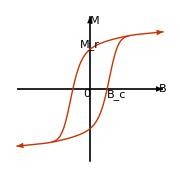

```mathematica
Block[{R=1.3,branch},
branch={Red,Arrowheads[{{0.001,0.6,Graphics[Line[Offset/@{{-2,-3},{2,0},{-2,3}}]]}}],Arrow[Table[{b,0.9Tanh[(5+3Tanh[2b])b]+0.1b},{b,-1,1,0.02}]]};
Graphics[{{Arrowheads[{{0.05,1}}],AbsoluteThickness[1.2],Arrow[ReIm@{-R,R}],Arrow[ReIm@{-ⅈ R,ⅈ R}],Text["0",{0,0},{1.5,1}],Text["\!\(B\)",{R,0},{0,1}],Text["\!\(M\)",{0,R},{-1.5,1}]},
Rotate[Translate[branch,{0.31,0.022}],#,{0,0}]&/@{0,π},
{Text["\!\(B\_c\)",{0.3,0},{-1,1}],Text["\!\(M\_r\)",{0,0.8},{1,0}]}},
ImageSize->180]]
```